# Rossler

The ODE is
	y'''[t]==-0.5y''[t]-y'[t]+y[t]-Sign[y[t]]
It (and it’s companion #11) are not quite smooth enough for our standard “Lipschitz” existence and uniqueness theorem!  This was addressed in a lecture. For now we are just going to approximate the solution numerically.

### Rossler with J=∇_x y and S=D_params y No Section!

Our system with a bunch of sensitivities but no section crossings is

```mathematica
Clear[f,dyf, dpf]
f[{a_,b_,c_}][{x_,y_,z_}]:={-y-z,x + a y,b + z(x-c)}
dyf[{a_,b_,c_}][{x_,y_,z_}]:=({{0, -1, -1}, {1, a, 0}, {z, 0, x-c}}) 
dpf[{a_,b_,c_}][{x_,y_,z_}]:=({{0, 0, 0}, {y, 0, 0}, {0, 1, -z}}) 
p={0.2,0.2,2.6};
TMax=123;
y0={5,0,1};
J0=IdentityMatrix[3];
S0=({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}});
{ySol,JSol,SSol}= NDSolveValue[ {
y'[t]==f[p][y[t]],
J'[t]==dyf[p][y[t]].J[t],
S'[t]==dpf[p][y[t]]+dyf[p][y[t]].S[t],
y[0]==y0,J[0]==J0,S[0]==S0},{y,J,S},{t,0,TMax}];
ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All]
TabView[{
"J-3D"->ParametricPlot3D[SingularValueList[JSol[t]],{t,0,TMax},
BoxRatios->{1, 1, 1}],
"S-3D"->ParametricPlot3D[SingularValueList[SSol[t]],{t,0,TMax},
BoxRatios->{1, 1, 1}],
"J"->LogPlot[SingularValueList[JSol[t],Tolerance->0],{t,0,TMax}],
"S"->LogPlot[SingularValueList[SSol[t]],{t,0,TMax}]
},3]
```

-Graphics3D-

1234

This has zoomed into an almost closed loop.

```mathematica
TStart=0.9TMax;
TabView[{
"y vs t"->Plot[ySol[t],{t, TStart,TMax}, GridLines->{Automatic,{p[[3]]}}],
"phase plot"->ParametricPlot3D[ySol[t],{t, TStart,TMax}]
},2]
```

12

### Rossler with J=∇_x y and S=D_params y Section Σ^-={y_1=c,-y_2-y_3<0}⊂ℝ^3!

Our parameterization is u={u_1,u_2}->{c,u_1,u_2}.   I modified the system to collect section points. I cheated by starting it on the section

```mathematica
Clear[f,dyf, dpf]
f[{a_,b_,c_}][{x_,y_,z_}]:={-y-z,x + a y,b + z(x-c)}
dyf[{a_,b_,c_}][{x_,y_,z_}]:=({{0, -1, -1}, {1, a, 0}, {z, 0, x-c}}) 
dpf[{a_,b_,c_}][{x_,y_,z_}]:=({{0, 0, 0}, {y, 0, 0}, {0, 1, -z}}) 
p={a,b,c}={0.2,0.2,2.6};
TMax=123;
y0={5,0,1};
J0=IdentityMatrix[3];
S0=({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}});
Clear[ySol]
SectionData = Reap[
{ySol,JSol,SSol}= NDSolveValue[ {
y'[t]==f[p][y[t]],
J'[t]==dyf[p][y[t]].J[t],
S'[t]==dpf[p][y[t]]+dyf[p][y[t]].S[t],
y[0]==y0,J[0]==J0,S[0]==S0,
WhenEvent[Indexed[y[t],1]-c <0,Sow[{t,y[t],J[t]}]]
(* I have no idea whay I had to use indexed instead of [[]] in here! *)
},{y,J,S},{t,0,TMax}];
]⟦2⟧;
tVals=SectionData⟦1,All,1⟧;
yVals=SectionData⟦1,All,2⟧;
JVals=SectionData⟦1,All,3⟧;
Show[
ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All],
ParametricPlot3D[{c,u1,u2},{u1,-2,5},{u2,0,8},PlotStyle->Opacity[0.5],Mesh->None],
Graphics3D[{Red, PointSize[0.02],Point[yVals]}]
]
```

-Graphics3D-

There is a once around loop in there.  We want to compute it!

```mathematica
TStart=0.96 TMax;
TabView[{
"Phase Plot"->ParametricPlot3D[ySol[t],{t, TStart, TMax}],
"y_1"->Plot[{ySol[t][[1]],c},{t, TStart, TMax}]
}]
{t, ySol[t]}/.FindRoot[ Indexed[ySol[t],1]==c,{t, 121}]
```

12

{121.212,{2.6,2.30017,3.3664}}

For c=2.6 the downward point on this last loop is roughly  {2.6, 2.30017, 3.3664}.  The question is how can we compute the accurately and/or without running the ODE solver out to infinity!

The answer is Newton’s method on for fixed points of the return map.  To do this we need to parameterize our section surface, build the return map and construct the gradient of the in-plane component of the return map in the parameterization.

### Rossler return map and gradient: Development Section Σ^-={y_1=c,-y_2-y_3<0}⊂ℝ^3!

The parameterization is u={u_1,u_2}->{c,u_1,u_2}.   The ODE system is modified to collect time t, position y, and sensitivity J after the first return. The parameterization make sure it starts on the section.  Here is how I developed the code.

```mathematica
Clear[f,dyf]
f[{a_,b_,c_}][{x_,y_,z_}]:={-y-z,x + a y,b + z(x-c)}
dyf[{a_,b_,c_}][{x_,y_,z_}]:=({{0, -1, -1}, {1, a, 0}, {z, 0, x-c}}) 
p={a,b,c}={0.2,0.2,2.6};
{u1,u2}={1,3};
y0={c,u1,u2};
{TMin,TMax}={0.001,123};
{tVal,yVal,JVal} = Reap[
{ySol,JSol}= NDSolveValue[ {
y'[t]==f[p][y[t]],
J'[t]==dyf[p][y[t]].J[t],
y[0]==y0,J[0]==IdentityMatrix[3],
WhenEvent[Indexed[y[t],1]-c <0,If[t>TMin, Sow[{t,y[t],J[t]}]; "StopIntegration"]]
(* I have no idea why I had to use indexed instead of [[]] in here! *)
},{y,J},{t,0,TMax}];
]⟦2,1,1⟧
```

{5.85182,{2.6,1.58443,0.625279},{{0.877895,0.508948,-0.615892},{-0.0444606,0.944188,0.476583},{0.50038,0.794778,-0.119296}}}

I am going to build a function out of this code snippet.

### Rossler return map and gradient: Function Section Σ^-={y_1=c,-y_2-y_3<0}⊂ℝ^3!

The parameterization is u={u_1,u_2}->{c,u_1,u_2}.   The ODE system is modified to collect time t, position y, and sensitivity J after the first return. The parameterization make sure it starts on the section.  Here is how I developed the code.

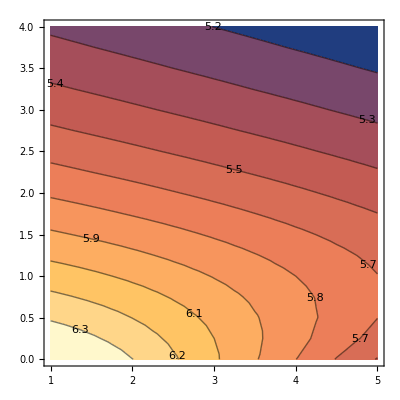

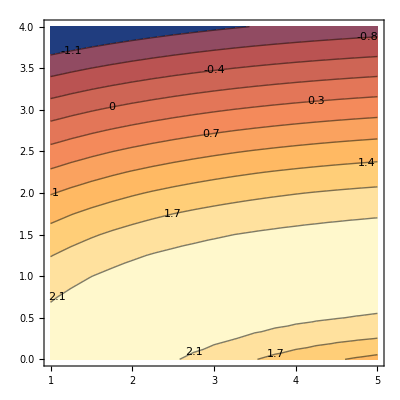

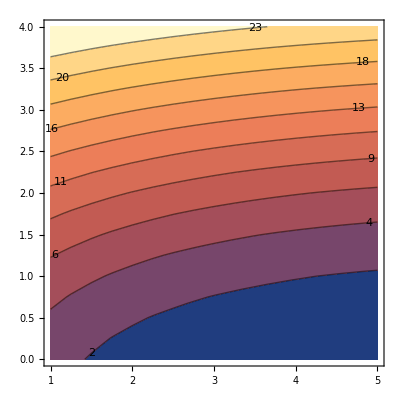

```mathematica
Clear[f,dyf,ReturnMapAndTimeAndJ]
f[{a_,b_,c_}][{x_,y_,z_}]:={-y-z,x + a y,b + z(x-c)}
dyf[{a_,b_,c_}][{x_,y_,z_}]:=({{0, -1, -1}, {1, a, 0}, {z, 0, x-c}}) 
ReturnMapAndTimeAndJ[{a_,b_,c_},{f_,dyf_}][{u1_,u2_}]:= Module[{y0,TMin=0.001,TMax=123,
tVal,yVal,JVal,ySol,JSol,y,J,t},
y0={c,u1,u2};
{tVal,yVal,JVal} = Reap[
{ySol,JSol}= NDSolveValue[ {
y'[t]==f[{a,b,c}][y[t]],
J'[t]==dyf[{a,b,c}][y[t]].J[t],
y[0]==y0,J[0]==IdentityMatrix[3],
WhenEvent[Indexed[y[t],1]-c <0,If[t>TMin, Sow[{t,y[t],J[t]}]; "StopIntegration"]]
(* I have no idea why I had to use indexed instead of [[]] in here! *)
},{y,J},{t,0,TMax}];
]⟦2,1,1⟧
]
p={0.2,0.2,2.6};
CoarseData=Table[
ReturnMapAndTimeAndJ[p,{f,dyf}][{u1,u2}],
{u1,1,5,0.25},
{u2,0,4,0.25}];
ListContourPlot[CoarseData⟦All,All,1⟧,
DataRange->{{1,5},{0,4}},
Contours->10,ContourLabels->True]
ListContourPlot[CoarseData⟦All,All,2,2⟧,
DataRange->{{1,5},{0,4}},
Contours->10,ContourLabels->True]
ListContourPlot[CoarseData⟦All,All,2,3⟧,
DataRange->{{1,5},{0,4}},
Contours->10,ContourLabels->True]
```

```mathematica
TableForm[CoarseData⟦All,All,1⟧]
```

6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371
6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371 | 6.07371

I am going to build a function out of this code snippet.